```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Bayesian*`*","Bayesian*`Private`*"];
<<BayesianInference`
Needs["CompiledFunctionTools`"]
```

```mathematica
defineInferenceProblem[]
```

{Data,Parameters,LogLikelihoodFunction,LogPriorPDFFunction,GeneratingDistribution,PriorDistribution,PriorDistribution,PriorPDF}

```mathematica
dist=CauchyDistribution;
testdata=RandomVariate[dist[0,1],10];
obj=defineInferenceProblem[
"Data"-> RandomVariate[dist[0,1],10],
"GeneratingDistribution" -> dist[mu, sigma],
"Parameters"->{{mu,-100,100},{sigma,0.01,100}},
"PriorDistribution"-> {"LocationParameter", "ScaleParameter"}
]
obj=generateStartingPoints[obj,25]
```

```mathematica
result=nestedSampling[
obj,
"MonteCarloSteps"->1000,
"MinMaxAcceptanceRate" ->{0.1,0.9}
]
result["ParameterExpectedValues"]
```

```mathematica
resultParallel=parallelNestedSampling[obj]
resultParallel["ParameterExpectedValues"]
```

```mathematica
Reverse@Values@result[["Samples",All,"AcceptanceRate"]]//ListPlot
```

```mathematica
ListLinePlot@Transpose@Reverse@Values@DeleteMissing@result[["Samples",All,"MeanEstimate"]]
```

```mathematica
ListLinePlot/@Transpose[Flatten/@Reverse@Values@DeleteMissing@result[["Samples",All,"CovarianceEstimate"]]]
```

#### GP

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Bayesian*`*","Bayesian*`Private`*"];
<<BayesianInference`
Needs["CompiledFunctionTools`"]
```

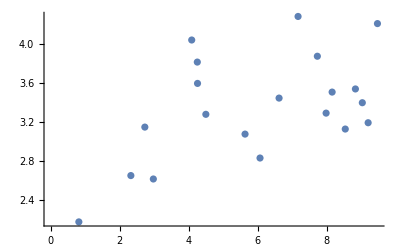

```mathematica
testdata=With[
{x=RandomReal[{0,10},20]},
x->
Function[
Sin[0.5 #]+0.4Sin[2 #]+0.4#+1+0.3*RandomVariate[NormalDistribution[],Length[x]]
][x+0.2*RandomVariate[NormalDistribution[],Length[x]]
]
];
ListPlot[List@@@Thread[testdata]]
```

```mathematica
obj=With[{vars={
{s1,0.01,100},
{l,0.05, 30},
{s0,0.02,20},
{m, -10,10}
}
},
gaussianProcessNestedSampling[
normalizeData[testdata],
Function[s1 *Boole[Subtract[#1,#2]^2<(6 l)^2] Exp[-Divide[Subtract[#1,#2]^2,l^2]]],
Function[s0],
Function[m],
{"ScaleParameter", "ScaleParameter","ScaleParameter", "LocationParameter"},
vars,
"SamplePoolSize" -> 25,
"MaxIterations"->10000,
"MinIterations"->20,
"TerminationFraction" -> 0.01,
"Monitor" -> True,
"Likelihood" -> "Custom",
"LikelihoodMaximum"->Automatic,
"ParallelRuns"->None
]
];
```

```mathematica
obj["Properties"]
```

```mathematica
obj["Samples"]//Dataset
```

#### Old

```mathematica
prob=ProbabilityDistribution[Exp[-x^2-y^2],{x,-∞,∞},{y,-∞,∞}];
RandomVariate[
prob,
10,
Method->{"MCMC","Thinning"->1,"InitialPoint"->{0,0},"BurnInPeriod"->Automatic,"InitialVariance"->{{10,0},{0,1}}}
]
```

{{-0.127448,-0.778248},{-0.0608503,-0.370009},{-0.0138355,-0.0816733},{0.0784999,0.484402},{0.126609,0.779385},{0.0466851,0.289793},{0.0466851,0.289793},{0.0200031,0.124782},{0.0364633,0.224422},{0.0963255,0.592652}}

```mathematica
Options[Random`Private`MCMC]
```

{Thinning→Automatic,InitialPoint→Automatic,InitialVariance→Automatic,BurnInPeriod→Automatic,MinEffectiveSampleSizeRatio→Automatic}

```mathematica
Attributes[Random`Private`MCMC]={Protected}
Definition[Random`Private`MCMC]
```

{Protected}

```mathematica
Names["Random`Private`*"]//TableForm
```

Random`Private`AcceptanceRejection
Random`Private`BTPE
Random`Private`CompoundSum
Random`Private`ConditionalStandardBallUniformDistribution
Random`Private`DevroyeBinomial
Random`Private`DoublesToInteger
Random`Private`H2PE
Random`Private`IntegerToDoubles
Random`Private`IntegerUniformDistribution
Random`Private`InternalComplexNormalDistribution
Random`Private`InternalExponentialDistribution
Random`Private`InternalGammaDistribution
Random`Private`InternalNormalDistribution
Random`Private`InternalPoissonDistribution
Random`Private`InternalStandardBallUniformDistribution
Random`Private`InternalStandardSimplexUniformDistribution
Random`Private`InternalStandardSphereUniformDistribution
Random`Private`InverseTransform
Random`Private`LogBinomialPDF
Random`Private`LogPoissonPDF
Random`Private`MapThreadMax
Random`Private`MapThreadMin
Random`Private`MCMC
Random`Private`MPZipfDistribution
Random`Private`MultiUniformDistribution
Random`Private`OrderingAndCounts
Random`Private`PositionsOf
Random`Private`RandomVariateVector
Random`Private`RejectionStandardBallUniformDistribution
Random`Private`SelectWithinRange
Random`Private`StructureQuantityArrayRandomVector
Random`Private`ZigguratExponentialDistribution
Random`Private`ZigguratNormalDistribution

```mathematica
Attributes[Random`Private`MCMC]={}
```

{}

```mathematica
Definition[Random`Private`MCMC]
```

Random`Private`MCMC[Statistics`RandomVariateDump`dist_,Statistics`RandomVariateDump`len_Integer,Statistics`RandomVariateDump`prec_,{Statistics`RandomVariateDump`thin_,Statistics`RandomVariateDump`initial_,Statistics`RandomVariateDump`ivar_,Statistics`RandomVariateDump`burnin_,Statistics`RandomVariateDump`minff_}]:=Module[{Statistics`RandomVariateDump`mineff,Statistics`RandomVariateDump`chainstate,Statistics`RandomVariateDump`mthd,Statistics`RandomVariateDump`head,Statistics`RandomVariateDump`contQ,Statistics`RandomVariateDump`sample},If[!(Statistics`RandomVariateDump`burnin===Automatic||Internal`NonNegativeIntegerQ[Statistics`RandomVariateDump`burnin]),Message[RandomVariate::optvg,BurnInPeriod,Statistics`RandomVariateDump`burnin,Automatic or a non-negative integer];Return[$Failed]];If[!(Statistics`RandomVariateDump`minff===Automatic||(Internal`RealValuedNumericQ[Statistics`RandomVariateDump`minff]&&0≤Statistics`RandomVariateDump`minff<1)),Message[RandomVariate::optvg,MinEffectiveSampleSizeRatio,Statistics`RandomVariateDump`minff,Automatic or a real number between 0 and 1];Return[$Failed]];If[!(Statistics`RandomVariateDump`thin===Automatic||Internal`PositiveIntegerQ[Statistics`RandomVariateDump`thin]),Message[RandomVariate::optvg,Thinning,Statistics`RandomVariateDump`thin,Automatic or a positive integer];Return[$Failed]];If[!(Statistics`RandomVariateDump`initial===Automatic||(Internal`RealValuedNumericQ[Statistics`RandomVariateDump`initial]&&Statistics`Library`DistributionDimensionality[Statistics`RandomVariateDump`dist]==1)||(Statistics`Library`RealVectorQ[Statistics`RandomVariateDump`initial]&&Statistics`Library`DistributionDimensionality[Statistics`RandomVariateDump`dist]==Length[Statistics`RandomVariateDump`initial])),Message[RandomVariate::mcmcin1,Statistics`RandomVariateDump`initial];Return[$Failed]];If[Statistics`RandomVariateDump`thin=!=Automatic&&Statistics`RandomVariateDump`minff=!=Automatic,Message[RandomVariate::szthin,Statistics`RandomVariateDump`minff]];If[Statistics`RandomVariateDump`minff===Statistics`RandomVariateDump`thin===Automatic,Statistics`RandomVariateDump`mineff=Statistics`RandomVariateDump`$EffectiveSampleSizeRatio,Statistics`RandomVariateDump`mineff=Statistics`RandomVariateDump`minff];Statistics`RandomVariateDump`mthd=AdaptiveMetropolis;Switch[Statistics`RandomVariateDump`dist,
_?Statistics`Library`ContinuousUnivariateDistributionQ,Statistics`RandomVariateDump`head=Statistics`RandomVariateDump`iMCMC1D;Statistics`RandomVariateDump`contQ=True,
_?Statistics`Library`ContinuousMultivariateDistributionQ,Statistics`RandomVariateDump`head=Statistics`RandomVariateDump`iMCMCND;Statistics`RandomVariateDump`contQ=True,
_?Statistics`Library`DiscreteUnivariateDistributionQ,Statistics`RandomVariateDump`head=Statistics`RandomVariateDump`iMCMC1D;Statistics`RandomVariateDump`contQ=False,
_?Statistics`Library`DiscreteMultivariateDistributionQ,Statistics`RandomVariateDump`head=Statistics`RandomVariateDump`iMCMCND;Statistics`RandomVariateDump`contQ=False,
_,Return[$Failed]];Statistics`RandomVariateDump`chainstate=Statistics`RandomVariateDump`head[Statistics`RandomVariateDump`dist,Statistics`RandomVariateDump`len,Statistics`RandomVariateDump`prec,Statistics`RandomVariateDump`mthd,{Statistics`RandomVariateDump`thin,Statistics`RandomVariateDump`initial,Statistics`RandomVariateDump`ivar,Statistics`RandomVariateDump`burnin,Statistics`RandomVariateDump`mineff},Statistics`RandomVariateDump`contQ];If[Statistics`RandomVariateDump`chainstate===$Failed,Message[RandomVariate::mcmc,Statistics`RandomVariateDump`dist,Statistics`RandomVariateDump`mthd];Return[$Failed]];Statistics`RandomVariateDump`sample=Statistics`RandomVariateDump`iSampleFromChain[Statistics`RandomVariateDump`chainstate,Statistics`RandomVariateDump`len,{Statistics`RandomVariateDump`mineff,Statistics`RandomVariateDump`thin}];If[Statistics`RandomVariateDump`sample===$Failed,Message[RandomVariate::mcmc,Statistics`RandomVariateDump`dist,Statistics`RandomVariateDump`mthd];Return[$Failed]];Statistics`RandomVariateDump`RandomSamplingExprStore[Statistics`RandomVariateDump`put[Statistics`RandomVariateDump`dist,MCobj,Statistics`RandomVariateDump`chainstate]];Statistics`RandomVariateDump`sample]
 
Options[Random`Private`MCMC]={Thinning→Automatic,InitialPoint→Automatic,InitialVariance→Automatic,BurnInPeriod→Automatic,MinEffectiveSampleSizeRatio→Automatic}

```mathematica
Statistics`RandomVariateDump`head[Statistics`RandomVariateDump`dist,Statistics`RandomVariateDump`len,Statistics`RandomVariateDump`prec,Statistics`RandomVariateDump`mthd,{Statistics`RandomVariateDump`thin,Statistics`RandomVariateDump`initial,Statistics`RandomVariateDump`ivar,Statistics`RandomVariateDump`burnin,Statistics`RandomVariateDump`mineff},Statistics`RandomVariateDump`contQ]
```

```mathematica
MarkovChainObject["Random walk Metrolopis-Hastings, Adaptive(Log)"]//First
```

<|StateData→{0.424262,0,0.,0.},IteratorFunction→(Statistics`MCMCSamplersDump`iAdaptiveMonteCarlo[#1,#2,Statistics`MCMCSamplersDump`ff$946,{0.5,10},#3,MachinePrecision,Statistics`MCMCSamplersDump`validDensityQ$946,{Statistics`MCMCSamplersDump`logQ$946,Statistics`MCMCSamplersDump`discreteQ$946}]&),RandomInputFunction→({RandomVariate[NormalDistribution[],#1,WorkingPrecision→MachinePrecision],Log[RandomReal[1,#1,WorkingPrecision→MachinePrecision]]}&),WorkingPrecision→MachinePrecision,MarkovChainType→Random walk Metrolopis-Hastings, Adaptive(Log),AcceptanceRate→None|>

```mathematica
Statistics`RandomVariateDump`iMCMCND//Definition
```

```mathematica
Statistics`RandomVariateDump`$InitialBurnIn
```

100